```mathematica
i1=Integrate[Exp[-s]Sin[nu s](1+b),{s,0,Infinity}]; (* Existence condition *)
```

```mathematica
ix=Integrate[Exp[-s]Cos[nu s](Exp[-lambda1 s]-1)(1+b),{s,0,Infinity}]; (* first axial integral *)
```

```mathematica
iy=Integrate[Exp[-s](Exp[-lambda2 s]-1)(1+b Cos[nu s]),{s,0,Infinity}]; (* second axial integral *)
```

```mathematica
(* Collect[FullSimplify[(lambda1 i1+nu ix)((1+lambda1)^2+nu^2)/(lambda1 nu (1+b))](1+nu^2),lambda1]
Collect[FullSimplify[(lambda2 i1-nu iy)((1+lambda2)^2+nu^2)(1+nu^2)(1+lambda2)/((1+b)nu lambda2)],lambda2] *)
```

```mathematica
ix
iy
```

ConditionalExpression[(1+b) (-1/(1+nu^2)+(1+lambda1)/((1+lambda1)^2+nu^2)),Abs[Im[nu]]<1&&Abs[Im[nu]]<1+Re[lambda1]]

ConditionalExpression[-1+1/(1+lambda2)-b/(1+nu^2)+(b (1+lambda2))/((1+lambda2)^2+nu^2),Abs[Im[nu]]<1&&Abs[Im[nu]]<1+Re[lambda2]]

```mathematica
(1+b) (-1/(1+nu^2)+(1+lambda1)/((1+lambda1)^2+nu^2))
```

```mathematica
(* stability *)
Collect[FullSimplify[(1 + nu/i1 ix/lambda1)((1+lambda1)^2+nu^2)],lambda1]/.lambda1->Subscript[λ, 1]/.nu->ν/.ν->1
Collect[FullSimplify[(1+nu/i1 iy/lambda2)(1+b) (1+lambda2) ((1+lambda2)^2+nu^2)/(1+b)],lambda2]/.lambda2->Subscript[λ, 2]/.nu->ν
```

ConditionalExpression[2+λ_1+λ_1^2,Re[λ_1]>-1]

ConditionalExpression[-(ν^2-2 b ν^2+ν^4)/(1+b)-((-1-b+ν^2-2 b ν^2) λ_2)/(1+b)-((2 (-1-b)+ν^2) λ_2^2)/(1+b)-((-1-b) λ_2^3)/(1+b),Abs[Im[ν]]<1&&Abs[Im[ν]]<1+Re[λ_2]]

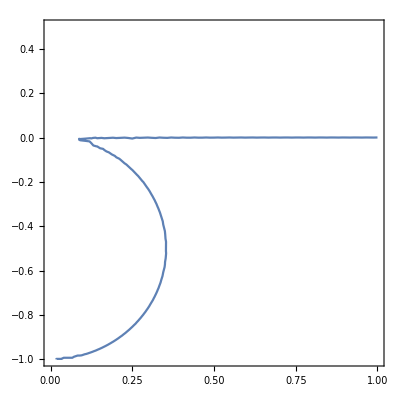

```mathematica
ContourPlot[{lambda1+nu/i1 ix==0},{nu,0,1},{lambda1,-1,.5}]
```